```mathematica
Off[General::"spell1"]
Off[General::"spell"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

## 1. Parameters for LCGT

### 1.1 Physical constants

```mathematica
hb=1.05457266912510183 10^-34;(* reduced Planck constant (J*s) *)
ω0=1.8 10^15;
c=2.99792458000000117*^8;(* speed of light (m/s) *)
Ω=2 π f;
kB=1.38*10^(-23);(* Boltzmann's constant (J/K) *)
g=9.8;(* acceleration of the gravity (m/s^2) *)
L=3000;
```

### 1.2 Laser

```mathematica
lambda=1064*10^(-9);(* wavelength (m) *)
```

### 1.3 Main cavity

```mathematica
l=3*10^3;(* length of cavity (m) *)
w1=3.5*10^(-2); (* ITM beam radius at mirrors (m) *)
w2=3.5*10^(-2); (* ETM beam radius at mirrors (m) *)
```

### 1.4 Mirror

```mathematica
rho=4.0*10^3;(* density (kg/m^3) *)
radius=11*10^(-2);(* radius (m); used to be 12.5cm *)
height=15*10^(-2);(* height (m) *)
mass=radius^2 π height rho;
Tm=290;(* temperature of mirror (K) *)
E0=4.0*10^(11);(* Young's modulus (Pa) *)
sigma = 0.29;(* Poisson ratio *)
Qmirror=10^(8);(* loss angle of material *)
```

```mathematica
kappa300=40;
Cth300=7.9 10^2;
alpha300=5.0 10^-6;
```

```mathematica
ρ=0.92; 
T=0.004;
```

### 1.5 Coating

```mathematica
Ncoa1=9;
Ncoa2=18;
```

```mathematica
Ys=7.2*10^10;(* Young's modulus for silica (Pa=N/m^2) *)
Yt=1.4*10^11;(* Young's modulus for Ta2O5 (Pa=N/m^2) *)
σs = 0.17;(* Poisson ratio for silica *)
σt = 0.23;(* Poisson ratio for Ta2O5 or sapphire *)
n1=1.45; (* Refraction index of silica *)
n2=2.07; (* Refraction index of tantala *)
dcoa1s=(Ncoa1+1)/4*10^(-6)/n1;(* thickness of ITM silica coating (m) *)
dcoa1t=Ncoa1/4*10^(-6)/n2;(* thickness of ITM tantala coating (m) *)
dcoa2s=(Ncoa2+1)/4*10^(-6)/n1;(* thickness of ETM silica coating (m) *)
dcoa2t=Ncoa2/4*10^(-6)/n2;(* thickness of ETM tantala coating (m) *)
ϕc1=3.0*10^(-4);(* loss angle of silica coating; new *)
ϕc2=5.0*10^(-4);(* loss angle of tantala coating; new *)
```

```mathematica
Cs=1.64 10^6;
κs=1.38/Cs;
αexps=5.1 10^-7;
Ct=2.1 10^6;
κt=33/Ct;
αexpt=3.6 10^-6;
```

### 1. Equations

#### Explanation

We solve the following set of equations:
-m3ω^2x3=-k3(1+ϕ3)(x3-x2)+F3
-m2ω^2x2=-k2(1+ϕ2)(x2-x1)+k3(1+ϕ3)(x3-x2)+F2
-m1ω^2x1=-k1(1+ϕ1)(x1)+k2(1+ϕ2)(x2-x1)+F1
to get
(x1
x2
x3)=(A1 | A2 | A3
B1 | B2 | B3
C1 | C2 | C3)^-1(F1/m1ω^2
F2/m2ω^2
F3/m3ω^2).
The 33 element of the 3x3 matrix of RHS is
(A1B2-A2B1)/(A1B2C3+A2B3C1+A3B1C2-A1B3C2-A2B1C3-A3B2C1).
We need the imaginary part.

#### Explanation 2

We solve the following set of equations:
-m3ω^2x3=-k3(1+ϕ3)(x3-x1)+F3
-m1ω^2x1=-k1(1+ϕ1)(x1)+k3(1+ϕ3)(x3-x1)+F1
to get
(x1
x3)=(A1 | A2
B1 | B2)^-1(F1/m1ω^2
F2/m3ω^2).
The 33 element of the 3x3 matrix of RHS is
A1/(A1B2-A2B1).
We need the imaginary part.

#### Ksusp

```mathematica
lsus=lsus3; 
dwire=2*r3;
Ewire=Y3;
ϕp=ϕS;
```

```mathematica
n=N3;
mass=m3;
```

```mathematica
Icwire=π/4 r3^4;(* moment of cross section (m^4) *)
```

```mathematica
ksus=Sqrt[(-mass*g/n+Sqrt[(mass*g/n)^2+4*Ewire*(1+I ϕp)*Icwire*rho*Pi*(dwire/2)^2*(2*Pi*f)^2])/(2*Ewire*(1+I ϕp)*Icwire)];
```

```mathematica
kele=Sqrt[(mass*g/n+Sqrt[(mass*g/n)^2+4*Ewire*(1+I ϕp)*Icwire*rho*Pi*(dwire/2)^2*(2*Pi*f)^2])/(2*Ewire*(1+I ϕp)*Icwire)];
```

```mathematica
Ksusp=n*Ewire*(1+I ϕp)Icwire*(ke ks (ke^2+ks^2)(Sinh[keL]ke Cos[ksL]+Cosh[keL] ks Sin[ksL]))/(2 ke ks(1-Cos[ksL] Cosh[keL])+(ke^2-ks^2) Sin[ksL] Sinh[keL])/.{ke->kele,ks->ksus,keL->kele lsus,ksL->ksus lsus};
```

#### Calculation

```mathematica
μ3=m3/m1;
AA1h=(ω1/ω)^2(1+I ϕ1)+μ3 Ksusp/(m3 ω^2);
AA2h=-μ3 Ksusp/(m3 ω^2);
BB1h=-μ3 Ksusp/(m3 ω^2);
BB2h=μ3 Ksusp/(m3 ω^2);
A1h=1-AA1h;
A2h=-AA2h;
B1h=-BB1h;
B2h=1-BB2h;
```

```mathematica
AA1=(ω1/ω)^2(1+I ϕ1)+μ1 (ω2/ω)^2(1+I ϕ2);
AA2=-μ1(ω2/ω)^2(1+I ϕ2);
AA3=0;
BB1=-(ω2/ω)^2(1+I ϕ2);
BB2=(ω2/ω)^2(1+I ϕ2)+μ2(ω3/ω)^2(1+I ϕ3);
BB3=-μ2(ω3/ω)^2(1+I ϕ3);
CC1=0;
CC2=-(ω3/ω)^2(1+I ϕ3);
CC3=(ω3/ω)^2(1+I ϕ3);
A1=1-AA1;
A2=-AA2;
A3=-AA3;
B1=-BB1;
B2=1-BB2;
B3=-BB3;
C1=-CC1;
C2=-CC2;
C3=1-CC3;
```

#### Calculation continued

```mathematica
μ1=m2/m1;
μ2=m3/m2;
```

```mathematica
μt=m2/(m2+m3);
```

```mathematica
I1=π/4 r1^4;
```

```mathematica
N1=4;
N3=4;
```

```mathematica
b1=2; (* number of bending points *)
```

```mathematica
D1=(b1*N1 √((m1 g/N1) Y1 I1))/(2m1 g lsus1); (* Saulson(1990); b is added. *)
```

```mathematica
ωh1=√(g/lsus1)√(1+D1);  (* This has been corrected. The second sqrt was missing! *)
ωh3=√(Ksusp/m3);
```

```mathematica
ωv1=√((π r1^2 Y1/lsus1)/(m1/4));
ωv2=√((2π fmg)^2/μt);
ωv3=√((π r3^2 Y3/lsus3)/(m3/4));
```

#### Parameters

```mathematica
kB=1.38*10^(-23);(* Boltzmann's constant (J/K) *)
g=9.8;(* acceleration of the gravity (m/s^2) *)
L=3000;
```

```mathematica
rho=4.0*10^3;(* density (kg/m^3) *)
```

```mathematica
ω=2π f;
m1=20.84;
m2=0.1;
m3=23;
fmg=14.5;
r1=0.0006/2;
r3=0.0016/2;
Y1=130*10^9; (* CuBe; *)
Y2=400*10^9; (* Sapphire *)
Y3=400*10^9; (* Sapphire *)
lsus1=0.261; 
lsus2=0.005; (* length of blade is unknown *)
lsus3=0.35;
ϕT=5 10^-6; (* CuBe *)
(* ϕS=2*10^-7; (* Sapphire *) *)
(* ϕS2=7*10^-7; (* Sapphire blade *) *)
ϕcl1=0*10^-3;
ϕcl2=0*10^-3;
ϕcl3=0*10^-3;
ϕh1=ϕT*T1/T3+ϕcl1*ω/ωv1; (* IM wire *)
ϕv1=ϕT*T1/T3+ϕcl1*ω/ωv1; (* IM wire *)
ϕv2=ϕS2*T2/T3+ϕcl2*ω/ωv2; (* Sapphire Blade *)
ϕv3=ϕS+ϕcl3*ω/ωv3; (* Sapphire Blade *)
T1=290; (* IM temperature is 16K *)
T2=290;
T3=290; (* TM temperature is 20K *)
VHC=1/200;
```

#### Suspension TE

```mathematica
beta300=(-35.7 10^6)/Y2^2(mass g)/(π (dwire/2)^2);
```

```mathematica
ϕtherm=(Ewire (alpha300-beta300)^2 T1)/(rho Cth300)(τd Ω)/(1+τd^2 Ω^2);
τd=(dwire^2 rho Cth300)/(13.55*kappa300);
ϕbulk=4*10^-10;
```

```mathematica
ϕS=ϕbulk(1+8 ds/dwire)+ϕtherm/.ds->200*10^-6; (* this ds is actually for silica *)
```

```mathematica
bladethickness=0.005; (* this is my guess *)
```

```mathematica
ϕtherm2=(Ewire (alpha300-beta300)^2 T1)/(rho Cth300)(τd2 Ω)/(1+τd2^2 Ω^2);
τd2=(bladethickness^2 rho Cth300)/(π^2*kappa300);
```

```mathematica
ϕS2=ϕbulk(1+6 ds/bladethickness)+ϕtherm2/.ds->200*10^-6; (* this ds is actually for silica *)
```

#### General calculation ref Ogawa et al and PPP

```mathematica
Tmath=({{T1, 0}, {0, T2}});
Tmat=({{T1, 0, 0}, {0, T2, 0}, {0, 0, T3}});
```

```mathematica
Z=I ω({{m1*A1h, m1*A2h}, {m3*B1h, m3*B2h}})/.{ω1->ωh1,ϕ1->ϕh1}; (* with violin modes *)
```

```mathematica
Fsq=4kB Re[Tmath.Z];
invD=Inverse[({{ω^2*A1h, ω^2*A2h}, {ω^2*B1h, ω^2*B2h}})]/.{ω1->ωh1,ϕ1->ϕh1};
```

```mathematica
Zv=-ω^2/(I ω)({{m1*A1, m1*A2, m1*A3}, {m2*B1, m2*B2, m2*B3}, {m3*C1, m3*C2, m3*C3}})/.{ω1->ωv1,ω2->ωv2,ω3->ωv3,ϕ1->ϕv1,ϕ2->ϕv2,ϕ3->ϕv3};
```

```mathematica
Fsqv=4kB Re[Tmat.Zv];
invDv=Inverse[({{ω^2*A1, ω^2*A2, ω^2*A3}, {ω^2*B1, ω^2*B2, ω^2*B3}, {ω^2*C1, ω^2*C2, ω^2*C3}})]/.{ω1->ωv1,ω2->ωv2,ω3->ωv3,ϕ1->ϕv1,ϕ2->ϕv2,ϕ3->ϕv3};
```

```mathematica
m0[1]=m1;
m0[2]=m2;
m0[3]=m3;
```

```mathematica
Sthh=(Fsq[[1]][[1]])/m0[1]^2 Abs[invD[[2]][[1]]]^2+(Fsq[[2]][[2]])/m0[3]^2 Abs[invD[[2]][[2]]]^2+(Fsq[[1]][[2]])/(m0[1]m0[3])2Re[invD[[2]][[1]]*Conjugate[invD[[2]][[2]]]];
```

```mathematica
Sthv=∑_(j=1)^3 (Fsqv[[j]][[j]])/m0[j]^2 Abs[invDv[[3]][[j]]]^2+(Fsqv[[1]][[2]])/(m0[1]m0[2])2Re[invDv[[3]][[1]]*Conjugate[invDv[[3]][[2]]]]+(Fsqv[[2]][[3]])/(m0[2]m0[3])2Re[invDv[[3]][[2]]*Conjugate[invDv[[3]][[3]]]]+(Fsqv[[1]][[3]])/(m0[1]m0[3])2Re[invDv[[3]][[1]]*Conjugate[invDv[[3]][[3]]]];
```

## 2. Seismic noise

```mathematica
hseistemp[f_]=2*2*Sqrt[(4.1*10^-17*f^-6.8)^2+(1.9*10^-16*f^-8)^2+(1.8*10^-18*f^-5.7)^2]; (* Multiplied by 2 for 4 mirrors and vertical seismic is added. *)
hGGN[f_]=1.2*10^-16/f^4/3000;
hseis[f_]=Sqrt[hseistemp[f]^2+hGGN[f]^2];
```

## 3. Thermal noise

### 3.1 Suspension (ITM+ETM) by PPP

```mathematica
hsusp[f_]=√(Abs[Sthh]+Abs[Sthv] VHC^2)*2/L;
```

### 3.2 Mirror

#### 3.2.1 Mirror (homogeneous structural damping)

```mathematica
hmirrorstr[f_]=(√2)/L*Sqrt[4*kB*Tm*(1-sigma^2)/(Sqrt[Pi]*E0*w1*Qmirror*2*Pi*f)+4*kB*Tm*(1-sigma^2)/(Sqrt[Pi]*E0*w2*Qmirror*2*Pi*f)];
```

#### 3.2.2 Mirror (thermoelastic damping)

```mathematica
Jhyper=1/Ωc^2(1-Re[ⅇ^((Ωc I)/2) ((1-Ωc I)(1- Erf[(√Ωc (1+I))/2]))])-√(1/(π Ωc^3));
Ωc=π Cs2 w0^2 f/kappa300/.Cs2->Cth300*rho;
```

```mathematica
hmirrorthermo2[f_]=(√2)/L √(((4 kB Tm^2 alpha300^2 (1+sigma)^2 w0)/(√π kappa300)*Jhyper/.w0->w1)+((4 kB Tm^2 alpha300^2 (1+sigma)^2 w0)/(√π kappa300)*Jhyper/.w0->w2));
```

#### 3.2.3 Mirror (coating: structural damping)

```mathematica
hmirrorcoa[f_]=(√2)/L √((4 kB Tm dcoa1s ϕc1)/(π w1^2 Ω)(Ys^2(1+sigma)^2(1-2sigma)^2+E0^2(1+σs)^2(1-2σs))/(E0^2 Ys(1-σs^2))+(4 kB Tm dcoa1t ϕc2)/(π w1^2 Ω)(Yt^2(1+sigma)^2(1-2sigma)^2+E0^2(1+σt)^2(1-2σt))/(E0^2 Yt(1-σt^2))+(4 kB Tm dcoa2s ϕc1)/(π w2^2 Ω)(Ys^2(1+sigma)^2(1-2sigma)^2+E0^2(1+σs)^2(1-2σs))/(E0^2 Ys(1-σs^2))+(4 kB Tm dcoa2t ϕc2)/(π w2^2 Ω)(Yt^2(1+sigma)^2(1-2sigma)^2+E0^2(1+σt)^2(1-2σt))/(E0^2 Yt(1-σt^2)));
```

#### 3.2.5 Total (ITM+ETM; low temperature; TO is ignored)

```mathematica
hmirror[f_]=Sqrt[hmirrorstr[f]^2+hmirrorthermo2[f]^2+hmirrorcoa[f]^2];
```

## 4. Optical readout noise (no ζ)

### 4.1 Additional parameter settings

```mathematica
m=mass; (* test mass (kg) *)
```

### 4.2 Basic equations for RSE

```mathematica
hSQL=√((8 hb)/(m Ω^2 L^2));

Sh=hSQL^2/(2 κ)(Abs[C11 Sin[ζ]+C21 Cos[ζ]]^2+Abs[C12 Sin[ζ]+C22 Cos[ζ]]^2+Abs[P12 Sin[ζ]+P22 Cos[ζ]]^2+Abs[P11 Sin[ζ]+P21 Cos[ζ]]^2+Abs[Q12 Sin[ζ]+Q22 Cos[ζ]]^2+Abs[Q11 Sin[ζ]+Q21 Cos[ζ]]^2+Abs[N11 Sin[ζ]+N21 Cos[ζ]]^2+Abs[N12 Sin[ζ]+N22 Cos[ζ]]^2+(Abs[M]*√Sadd)^2)/(τ^2 Abs[D1sig Sin[ζ]+D2sig Cos[ζ]]^2);
```

```mathematica
M=1+ρ^2 Exp[4 I β]-2ρ(Cos[2ϕ]+κ/2 Sin[2ϕ])Exp[2 I β]+λSR ρ(-ρ Exp[2 I β]+Cos[2ϕ]+κ/2 Sin[2ϕ])Exp[2 I β]+ϵ ρ(2 Cos[β]^2(-ρ Exp[2 I β]+Cos[2ϕ])+κ/2(3+Exp[2 I β])Sin[2ϕ])Exp[2 I β];
C11=√(1-λPD)((1+ρ^2) (Cos[2 ϕ]+κ/2 Sin[2 ϕ])-2 ρ Cos[2 β]-1/4 ϵ(-2(1+Exp[2 I β])^2 ρ+4(1+ρ^2)Cos[β]^2 Cos[2ϕ]+(3+Exp[2 I β])κ(1+ρ^2)Sin[2 ϕ])+λSR(Exp[2 I β]ρ-1/2(1+ρ^2)(Cos[2 ϕ]+κ/2 Sin[2ϕ])));
C12=√(1-λPD)τ^2 ( -Sin[2 ϕ]-κ  Sin[ϕ]^2+1/2 ϵ Sin[ϕ]((3+Exp[2 I β])κ Sin[ϕ]+4 Cos[β]^2 Cos[ϕ])+1/2 λSR(Sin[2ϕ]+κ Sin[ϕ]^2));
C21=√(1-λPD)τ^2 (Sin[2 ϕ]-κ  Cos[ϕ]^2+1/2 ϵ Cos[ϕ]((3+Exp[2 I β])κ Cos[ϕ]-4 Cos[β]^2 Sin[ϕ])+1/2 λSR(-Sin[2ϕ]+κ Cos[ϕ]^2)) ;
C22=C11;
D1sig=√(1-λPD)(-(1+ρ Exp[2 I β]) Sin[ϕ]+1/4 ϵ(3+ρ+2ρ Exp[4 I β]+(1+5ρ)Exp[2 I β])Sin[ϕ]+1/2 λSR Exp[2 I β]ρ Sin[ϕ]);
D2sig=√(1-λPD)(-(-1+ρ Exp[2 I β]) Cos[ϕ]+1/4 ϵ(-3+ρ+2ρ Exp[4 I β]+(-1+5ρ)Exp[2 I β])Cos[ϕ]+1/2 λSR Exp[2 I β]ρ Cos[ϕ]);
P11=1/2 √(1-λPD)√λSR τ(-2ρ Exp[2 I β]+2Cos[2ϕ]+κ Sin[2ϕ]);
P12=-√(1-λPD)√λSR τ Sin[ϕ](2Cos[ϕ]+κ Sin[ϕ]);
P21=√(1-λPD)√λSR τ Cos[ϕ](2Sin[ϕ]-κ Cos[ϕ]);
P22=P11;
Q11=√λPD(Exp[-2 I β]+ρ^2 Exp[2 I β]-ρ(2 Cos[2ϕ]+κ Sin[2 ϕ])+1/2 ϵ ρ(Exp[-2 I β]Cos[2ϕ]+Exp[2 I β](-2ρ-2ρ Cos[2 β]+Cos[2ϕ]+κ Sin[2ϕ])+2 Cos[2ϕ]+3 κ Sin[2ϕ])-1/2 λSR ρ(2ρ Exp[2 I β]-2 Cos[2ϕ]-κ Sin[2ϕ]));
Q12=0;
Q21=0;
Q22=Q11;
N11=√(1-λPD)√(ϵ/2)τ(κ(1+ρ Exp[2 I β])Sin[ϕ]+2Cos[β](Exp[-I β]Cos[ϕ]-ρ Exp[I β](Cos[ϕ]+κ Sin[ϕ])));
N12=-√(1-λPD)√(2 ϵ)τ(Exp[-I β]+ρ Exp[I β])Cos[β]Sin[ϕ];
N22=-√(1-λPD)√(2 ϵ)τ(-Exp[-I β]+ρ Exp[I β])Cos[β]Cos[ϕ];
N21=√(1-λPD)√(ϵ/2)τ(-κ(1+ρ)Cos[ϕ]+2Cos[β](Exp[-I β]+ρ Exp[I β])Cos[β] Sin[ϕ]);
```

```mathematica
γ=T c/(4 L);(* cavity pole *)
τ=√(1-ρ^2); (* SRM transmittance *)
β=ArcTan[Ω/γ]; (* phase shift in the arm cavity *)
κ=(2 (I0/ISQL) γ^4)/(Ω^2 (γ^2+Ω^2)); (* coefficient that shows how much the mirror moves *)
ISQL=(m L^2 γ^4)/(4 ω0); (* the power with which the quantum noise reaches the SQL at the cavity pole frequency *)
```

### 4.3 Loss parameters

```mathematica
roundtriploss=100*10^(-6); (* ppm *)
ϵ = 2/T*roundtriploss; (* loss parameter of arms defined in KLMTV paper *)
λSR =0.002; (* loss in power at the signal recycling mirror *)
λPD=0.1;
Sadd= 0*(π^2/8 - 1);
```

## 6. Optimal Result

```mathematica
param={ϕ->π/180*86.5,I0->550};
```

### 6.1 Parameters

```mathematica
Gravity=6.673*10^(-11);(* Gravitational constant (m^3/Kg/s^2) *)
solarmass=1.989*10^(30);(* mass of Sun (Kg) *)
Mpc=365.2422*24*60*60*c*3.26*10^6;(* 1 Mpc (m) *)
```

```mathematica
mass1=1.4*solarmass;(* mass of a compact object (Kg) *)
mass2=1.4*solarmass;(* mass of other compace object (Kg) *)
mtotal=mass1+mass2;(* total moss of binary system (Kg) *)
mreduce=mass1*mass2/mtotal;(* reduced mass of binary system (Kg) *)
fmin=10;(* low cut off frequency of integral (Hz) *)
fmax=c^3/(6^(3/2)*Pi*Gravity*mtotal);(* high cut off frequency of integral; ISCO (Hz) *)
SNR=8;(* threshold of Signal to Noise Ratio *)
```

### 6.2 Integration

```mathematica
fmid=300;
Nini=60;
Nmid=20;
```

```mathematica
integ=(∑_(ff=1)^Nini (1/(f^(7/3)*(Sh+hsusp[f]^2+hmirror[f]^2+hseis[f]^2))*(fmid-fmin)/Nini/.f->fmin+(fmid-fmin)*(ff-0.5)/Nini)/.T->OptT)+(∑_(ff=1)^Nmid (1/(f^(7/3)*(Sh+hsusp[f]^2+hmirror[f]^2+hseis[f]^2))*(fmax-fmid)/Nmid/.f->fmid+(fmax-fmid)*(ff-0.5)/Nmid)/.T->OptT);
```

### 6.3 Optimal DC readout phase

```mathematica
RangeDRSE3deg=FindMaximum[(1/SNR)/Sqrt[2]*2*(Gravity/c^3)^(5/6)*c*(5/96*mreduce)^(1/2)*(mtotal/Pi^2)^(1/3)*Sqrt[4*integ]/Mpc/.param,{ζ,0.01,1.57}];
```

```mathematica
OptZeta=ζ/.RangeDRSE3deg[[2]][[1]]
```

-0.684445

Sky average (new); 0.442478 is given by Kanda-san.

```mathematica
(1/SNR)*2*0.442478*(Gravity/c^3)^(5/6)*c*(5/96*mreduce)^(1/2)*(mtotal/Pi^2)^(1/3)*Sqrt[4*integ]/Mpc/.{ϕ->π/2,I0->550}/.ζ->π/2
```

18.0751

```mathematica
(1/SNR)*2*0.442478*(Gravity/c^3)^(5/6)*c*(5/96*mreduce)^(1/2)*(mtotal/Pi^2)^(1/3)*Sqrt[4*integ]/Mpc/.param/.ζ->OptZeta
```

16.1001

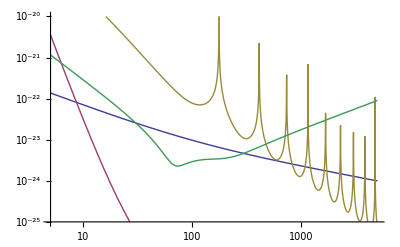

```mathematica
LogLogPlot[{hmirror[f],hseis[f],√(Abs[Sthh]+0*Abs[Sthv] VHC^2)*2/L,√Sh/.param/.ζ->OptZeta},{f,5,5000},PlotRange->{10^-25,10^-20}]
```

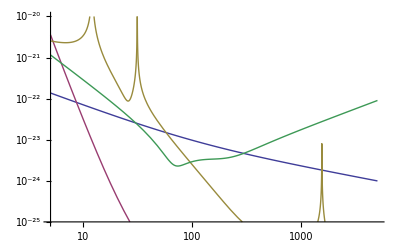

```mathematica
LogLogPlot[{hmirror[f],hseis[f],√(0*Abs[Sthh]+Abs[Sthv] VHC^2)*2/L,√Sh/.param/.ζ->OptZeta},{f,5,5000},PlotRange->{10^-25,10^-20}]
```

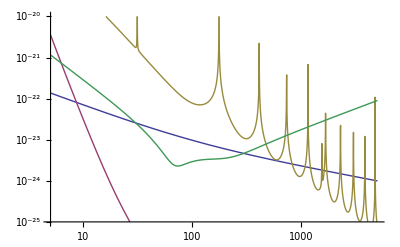

```mathematica
LogLogPlot[{hmirror[f],hseis[f],hsusp[f],√Sh/.param/.ζ->OptZeta},{f,5,5000},PlotRange->{10^-25,10^-20}]
```

## 7. Data output

```mathematica
logDataOutput[filename_String, X_, {imin_, imax_}] :=
  Module[{strm},
    strm = OpenWrite[filename];
    Do[
      Do[
        Module[{},
          Map[writeList[strm, #] &, { x , X} /. x -> (10^i) 10^ j];
          writeListn[strm];
          ],
        {i, 0.001, 1, 0.001}
        ],
      {j, imin, imax}
      ];
    Close[strm];
    ]
```

```mathematica
writeList[strm_, dat_] :=
  WriteString[strm, ToString[FortranForm[dat]], " "];
```

```mathematica
writeListn[strm_] :=
  WriteString[strm, "\n"];
```

```mathematica
logDataOutput["QN.dat",√Sh/.ζ->OptZeta/.param/.{f->x},{0,3}](* ζ was wrong before 170521!! *)
```

```mathematica
logDataOutput["hmirror.dat",hmirror[f]/.{f->x},{0,3}]
```

```mathematica
logDataOutput["hsusp.dat", hsusp[f] /. {f -> x}, {0, 3}]
```

```mathematica
logDataOutput["hseis.dat",hseis[f]/.{f->x},{0,3}]
```

```mathematica
logDataOutput["hSQL.dat",hSQL/.{f->x},{0,3}]
```

```mathematica
logDataOutput["total.dat",√(Sh+hmirror[f]^2+hseis[f]^2+hsusp[f]^2)/.ζ->OptZeta/.param/.{f->x},{0,3}] (* ζ was wrong before 170521!! *)
```